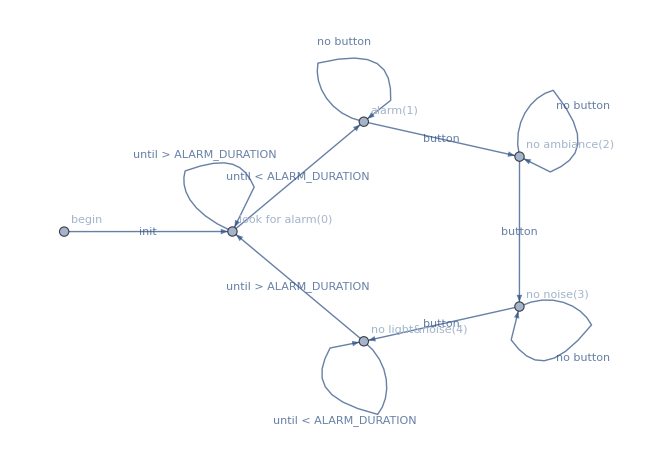

```mathematica
Graph[{Labeled["begin"->"look for alarm(0)","init"],Labeled["look for alarm(0)"->"look for alarm(0)","until > ALARM_DURATION"],Labeled["look for alarm(0)"->"alarm(1)","until < ALARM_DURATION"],Labeled["alarm(1)"->"alarm(1)","no button"],Labeled["alarm(1)"->"no ambiance(2)","button"],Labeled["no ambiance(2)"->"no ambiance(2)","no button"],Labeled["no ambiance(2)"->"no noise(3)","button"],Labeled["no noise(3)"->"no noise(3)","no button"],Labeled["no noise(3)"->"no light&noise(4)","button"],Labeled["no light&noise(4)"->"no light&noise(4)","until < ALARM_DURATION"],Labeled["no light&noise(4)"->"look for alarm(0)","until > ALARM_DURATION"]},VertexLabels->"Name"]
```